## Scientific Programming 3

Recall some shortcuts:
f @@ expr :Apply[f,expr] replaces head by f
f /@ expr -> Map[f, expr] applies f to each element on the first level
// eg: // N to apply N[ ... ]
/. to access parts of ‘soln’ eg: ‘y[t] /. soln’
expr /. rule : applies a rule to transform each subpart of an expression

Structure of Mathematica

### Numbers

```mathematica
Head/@{3,22/7,3.14,2.34+2.09 ⅈ, π}
```

{Integer,Rational,Real,Complex,Symbol}

```mathematica
FullForm/@{3,22/7,3.14,2.34+2.09 ⅈ, π}
```

{3,Rational[22,7],3.14,Complex[2.34,2.09],Pi}

```mathematica
7==7.0
```

True

SameQ (===) returns True if two expressions are IDENTICAL

```mathematica
7===7.0 (*SameQ*)
```

False

```mathematica
x==7
```

x==7

```mathematica
x===7
```

False

Note that we can evaluate numerically an expression using // N

```mathematica
{ⅇ^π,π^ⅇ}//N
```

{ⅇ^π,π^ⅇ}

```mathematica
ⅇ^π> π^ⅇ
```

True

```mathematica
ⅇ^π< π^ⅇ
```

False

```mathematica
?IntegerDigits
?FromDigits
```

IntegerDigits[n] gives a list of the decimal digits in the integer n. 
IntegerDigits[n,b] gives a list of the base b digits in the integer n. 
IntegerDigits[n,b,len] pads the list on the left with zeros to give a list of length len. 
IntegerDigits[n,MixedRadix[blist]] uses the mixed radix with list of bases blist.

FromDigits[list] constructs an integer from the list of its decimal digits. 
FromDigits[list,b] takes the digits to be given in base b. 
FromDigits[list,MixedRadix[blist]] uses the mixed radix with list of bases blist. 
FromDigits[string] constructs an integer from a string of digits.
FromDigits[string,Roman] constructs an integer from Roman numerals.

```mathematica
IntegerDigits[3569]
```

{3,5,6,9}

```mathematica
FromDigits[%]
```

3569

```mathematica
N[EulerGamma]
```

0.577216

```mathematica
?RealDigits
```

RealDigits[x] gives a list of the digits in the approximate real number x, together with the number of digits that are to the left of the decimal point. 
RealDigits[x,b] gives a list of base-b digits in x. 
RealDigits[x,b,len] gives a list of len digits. 
RealDigits[x,b,len,n] gives len digits starting with the coefficient of b^n.

```mathematica
RealDigits[%]
```

{{5,7,7,2,1,5,6,6,4,9,0,1,5,3,2,9},0}

```mathematica
RealDigits[N[π,100]]
```

{{3,1,4,1,5,9,2,6,5,3,5,8,9,7,9,3,2,3,8,4,6,2,6,4,3,3,8,3,2,7,9,5,0,2,8,8,4,1,9,7,1,6,9,3,9,9,3,7,5,1,0,5,8,2,0,9,7,4,9,4,4,5,9,2,3,0,7,8,1,6,4,0,6,2,8,6,2,0,8,9,9,8,6,2,8,0,3,4,8,2,5,3,4,2,1,1,7,0,6,8},1}

```mathematica
RealDigits[325.23]
```

{{3,2,5,2,3,0,0,0,0,0,0,0,0,0,0,0},3}

```mathematica
RealDigits[N[π,10],2]
```

{{1,1,0,0,1,0,0,1,0,0,0,0,1,1,1,1,1,1,0,1,1,0,1,0,1,0,1,0,0,0,1,0,0},2}

### Precision and Accuracy

```mathematica
e=N[ⅇ]
```

2.71828

```mathematica
FullForm[e]
```

2.71828

```mathematica
x=1.5
```

1.5

```mathematica
FullForm[x]
```

1.5

```mathematica
1.5 π
```

4.71239

```mathematica
N[1.5 π,100]
```

4.71239

```mathematica
N[3/2 π,100]
```

4.712388980384689857693965074919254326295754099062658731462416888461724609429313497942052238013175602

```mathematica
2/3%
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
%==N[π,100]
```

True

```mathematica
x=1.5``100
```

1.5

```mathematica
N[x π,100]===N[3/2 π,100]
```

True

```mathematica
N[x π,200]===N[3/2 π,200]
```

True

```mathematica
N[x π,200]
```

4.712388980384689857693965074919254326295754099062658731462416888461724609429313497942052238013175602

```mathematica
N[3/2 π,200]
```

4.7123889803846898576939650749192543262957540990626587314624168884617246094293134979420522380131756019732221297699234599706407669143258733475880391121927216761754261540529077816583394669344234323955729

```mathematica
?N
```

N[expr] gives the numerical value of expr. 
N[expr,n] attempts to give a result with n-digit precision.

```mathematica
Precision[x]
```

100.176

```mathematica
Accuracy[x]
```

100.

```mathematica
?Precision
?Accuracy
```

Precision[x] gives the effective number of digits of precision in the number x.

Accuracy[x] gives the effective number of digits to the right of the decimal point in the number x.

```mathematica
Precision[3/2]
```

∞

### Solving differential equations

```mathematica
eq[t_]:=y''[t]-1/5(1-y[t]^2)y'[t] + y[t]
```

```mathematica
soln=NDSolve[{eq[t]==0,y[0]==1,y'[0]==0},y,{t,0,30}]
```

{{y→InterpolatingFunction[…]}}

To access parts of the solution, use /.

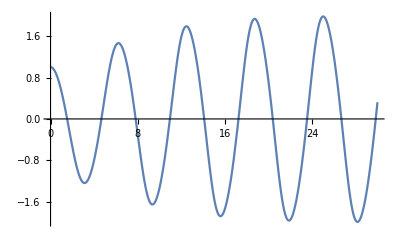

```mathematica
Plot[y[t]/.soln,{t,0,30},
         ImageSize->400]
```

```mathematica
y'[30]/.soln
```

{2.0361}

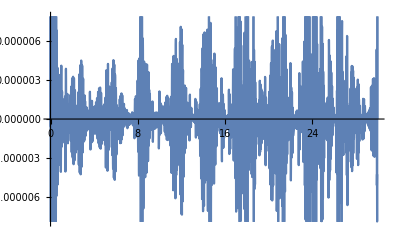

```mathematica
Plot[eq[t]/.soln,{t,0,30},
         ImageSize->400]
```

```mathematica
soln40=
NDSolve[{eq[t]==0,y[0]==1,y'[0]==0},y,{t,0,30},
                WorkingPrecision->40, PrecisionGoal->35]
```

{{y→InterpolatingFunction[{{0, 30.00000000000000000000000000000000000000}}, <>]}}

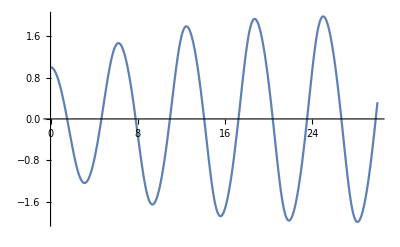

```mathematica
Plot[y[t]/.soln40,{t,0,30},
         ImageSize->400]
```

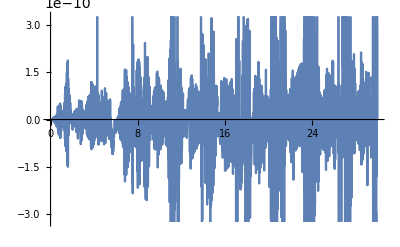

```mathematica
Plot[eq[t]/.soln40,{t,0,30},
         ImageSize->400]
```

```mathematica
Clear[x,f]
```

```mathematica
eq=4 x(x-1) f''[x]+(10 x-4) f'[x]+2 f[x]-(3 (x-3))/(1-x)^(3/2)
```

-(3 (-3+x))/(1-x)^(3/2)+2 f[x]+(-4+10 x) f'[x]+4 (-1+x) x f''[x]

We want a solution f[x] that vanishes at x=0.

```mathematica
fsoln=DSolve[{eq==0,f[0]==0},f,x]⟦1⟧//FullSimplify
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

Let us try again, and temporarily drop the condition f[0] = 0.

```mathematica
fsoln=DSolve[eq==0,f,x]⟦1⟧//FullSimplify
```

{f→Function[{x},C[1]/(√(1-x))+(C[2] (Log[1-√(1-x)]-Log[1+√(1-x)]))/(√(1-x))-1/(2 (-1+x))3 (√(1-x) Log[1-√(1-x)]+√(1-x) Log[1+√(1-x)]-2 √(1-x) Log[1-x])]}

```mathematica
fser=Series[(f/.fsoln)⟦2⟧,{x,0,1}]
```

(C[1]-2 C[2] Log[2]+(3 Log[x])/2+C[2] Log[x])+1/4 (12+2 C[1]+2 C[2]-4 C[2] Log[2]+3 Log[x]+2 C[2] Log[x]) x+O[x]^2

```mathematica
fser/.{C[2]->-3/2, C[1]-> -3Log[2]}
```

(9 x)/4+O[x]^2

```mathematica
F=(f/.fsoln)⟦2⟧/.{C[2]->-3/2, C[1]-> -3Log[2]} //Simplify
```

(3 (Log[1+√(1-x)]-Log[2-2 x]))/(√(1-x))

```mathematica
Series[F,{x,0,10}]
```

(9 x)/4+(75 x^2)/32+(147 x^3)/64+(2283 x^4)/1024+(22143 x^5)/10240+(86021 x^6)/40960+(1171733 x^7)/573440+(7309677 x^8)/3670016+(14274301 x^9)/7340032+(55835135 x^10)/29360128+O[x]^11

A project to do with the periods of a CY manifold

```mathematica
Tpoly[x_,y_]:=x+1/x+y+1/y+x/y+y/x
```

```mathematica
?Coefficient
```

Coefficient[expr,form] gives the coefficient of form in the polynomial expr. 
Coefficient[expr,form,n] gives the coefficient of form^n in expr.

```mathematica
Subscript[T, k_]:=Subscript[T, k]=
Coefficient[
Coefficient[Tpoly[x,y]^k,x,0],
                        y,0] (*the coefficient of x^0 y^0*)
```

```mathematica
?OddQ
```

OddQ[expr] gives True if expr is an odd integer, and False otherwise.

```mathematica
Subscript[α, n_]:= Subscript[α, n]=
If[OddQ[n],2Sum[Binomial[n,k] Subscript[T, n-k] Subscript[T, k],{k,0,(n-1)/2}],2Sum[Binomial[n,k] Subscript[T, n-k] Subscript[T, k],{k,0,n/2-1}]+Binomial[n,n/2] Subscript[T, n/2]^2
       ]
```

```mathematica
Table[Subscript[α, n],{n,0,50}]
```

{1,0,12,24,396,2160,23160,186480,1845900,17213280,171575712,1703560320,17365421304,178323713568,1856554560432,19487791106784,206411964321420,2201711191213248,23642813637773616,255355132936441824,2772650461148938656,30248675037382538880,331438542846964180992,3645985314663912489984,40253352687777620374776,445899348810135736176960,4954599887270237905852800,55210013720527863783880320,616845490089371010724497840,6908835039102833099223965760,77558935621320663634645169760,872555336075039351141820542400,9836256654406990510063112404620,111093683696857593088076506055040,1256964832153899565798063964625360,14245801154241460321451736436267680,161711184920698116201513043068894000,1838422802677352902944026880120269760,20929968050634158361809598843821082720,238604084297865887503634354739682226880,2723604302705399110711864482680203408800,31127182673212368692213826730815487238400,356155829380376900900913291081937387488000,4079634680295870734083713299360651118873600,46780149321943165896822459952777274423385600,536958394984483586022362225192235106645985280,6169348420937264128969792709201188166008089600,70947930272537334350509861861788754738180700160,816629740093680630102475274822880521200882128120,9407624323260315606435813085689677006965402097280,108464914912610947331756997308308146813500741423712}

```mathematica
Subscript[ϖ, 0]:=Sum[Subscript[α, n] φ^n,{n,0,50}]+O[φ]^51
```

```mathematica
? Nest
```

Nest[f,expr,n] gives an expression with f applied n times to expr.

```mathematica
θ[fn_]:=φ D[fn,φ] (*i.e. φ ∂fn/∂φ*)
θ[fn_,m_]:=Nest[θ,fn,m] (*i.e. applies (φ∂/∂φ)^m fn*)
```

```mathematica
θ[φ^n]
```

n φ^n

```mathematica
θ[φ^n,4]
```

n^4 φ^n

```mathematica
Subscript[R, j_,kmax_]:=Sum[Subscript[r, j,k] φ^k,{k,0,kmax}] (*Subscript[r, j,k] φ^k summed over k to kmax*)
```

```mathematica
L[fn_,kmax_]:=Sum[Subscript[R, j,kmax] θ[fn,j],{j,0,4}] (*L[f]= Subscript[R, j](φ∂/(∂φ))^j f =Subscript[r, j,k] φ^k(φ∂/(∂φ))^j f  summed over j but only to j=4, and over k to kmax*)
```

```mathematica
?Normal
```

Normal[expr] converts expr to a normal expression from a variety of special forms. 
Normal[expr,h] converts objects with head h in expr to normal expressions.
Normal[expr,{h_1,h_2,…}] converts objects with head h_i to normal expressions.

```mathematica
With[{kmax=3},
CoefficientList[
Normal[L[Subscript[ϖ, 0],kmax]],φ]  (*Subscript[α, n] Subscript[r, j,k] φ^k(φ∂/(∂φ))^j φ^n -> look at φ^i coeffs*)
          ]
```

```mathematica
Length[%]
```

51

```mathematica
Solve[%%==0]⟦1⟧
```

{{r_(0,0)→0,r_(0,1)→0,r_(0,2)→0,r_(0,3)→0,r_(1,0)→0,r_(1,1)→0,r_(1,2)→0,r_(1,3)→0,r_(2,0)→0,r_(2,1)→0,r_(2,2)→0,r_(2,3)→0,r_(3,0)→0,r_(3,1)→0,r_(3,2)→0,r_(3,3)→0,r_(4,0)→0,r_(4,1)→0,r_(4,2)→0,r_(4,3)→0}}

```mathematica
Rlist:=
Module[{kmax=3,Rsoln,tempRlist={0,0,0,0,0}},
While[tempRlist=={0,0,0,0,0},
kmax++;
Rsoln=
Solve[
CoefficientList[
Normal[L[Subscript[ϖ, 0],kmax]],φ] ==0]⟦1⟧;
tempRlist=Simplify[Table[Subscript[R, j,kmax],{j,0,4}]/.Rsoln]];
   tempRlist ]
```

```mathematica
Rlist
```

{1/36 φ^2 (36+9 φ-6182 φ^2+284 φ^3+132120 φ^4-130464 φ^5+34560 φ^6) r_(0,2),1/1728 φ (9+5532 φ-1584 φ^2-679952 φ^3+166288 φ^4+12372480 φ^5-12745728 φ^6+3456000 φ^7) r_(0,2),1/1728 φ (39+6917 φ-5250 φ^2-552220 φ^3+274360 φ^4+7771104 φ^5-8581248 φ^6+2419200 φ^7) r_(0,2),1/432 φ (15+1025 φ-1170 φ^2-47572 φ^3+36464 φ^4+473904 φ^5-577152 φ^6+172800 φ^7) r_(0,2),((3-2 φ)^2 (-1+4 φ+115 φ^2-10 φ^3-2664 φ^4-864 φ^5+17280 φ^6) r_(0,2))/1728}

```mathematica
Subscript[R, j_]:=Rlist⟦j+1⟧/.Subscript[r, 0,2]:> 1728
```

```mathematica
Subscript[R, 4]
```

(3-2 φ)^2 (-1+4 φ+115 φ^2-10 φ^3-2664 φ^4-864 φ^5+17280 φ^6)

```mathematica
Factor[Subscript[R, 4]]
```

(-3+2 φ)^2 (-1+3 φ) (-1+4 φ) (1+4 φ) (1+5 φ) (1+6 φ) (-1+12 φ)

```mathematica
Exp[-1/2 Integrate[Subscript[R, 3]/(φ Subscript[R, 4]),φ]]//Factor
```

(-3+2 φ)/(4 (-1+3 φ) (-1+4 φ) (1+4 φ) (1+5 φ) (1+6 φ) (-1+12 φ))

```mathematica
ℒ[fn_]:=Sum[Subscript[R, j] θ[fn,j],{j,0,4}]
```

```mathematica
ℒ[Subscript[ϖ, 0]]
```

O[φ]^51

```mathematica
Lpoly=Sum[Subscript[R, j] ξ^j,{j,0,4}]
```

ξ^4 (3-2 φ)^2 (-1+4 φ+115 φ^2-10 φ^3-2664 φ^4-864 φ^5+17280 φ^6)+48 φ^2 (36+9 φ-6182 φ^2+284 φ^3+132120 φ^4-130464 φ^5+34560 φ^6)+4 ξ^3 φ (15+1025 φ-1170 φ^2-47572 φ^3+36464 φ^4+473904 φ^5-577152 φ^6+172800 φ^7)+ξ^2 φ (39+6917 φ-5250 φ^2-552220 φ^3+274360 φ^4+7771104 φ^5-8581248 φ^6+2419200 φ^7)+ξ φ (9+5532 φ-1584 φ^2-679952 φ^3+166288 φ^4+12372480 φ^5-12745728 φ^6+3456000 φ^7)

```mathematica
Collect[Lpoly,φ,Simplify]
```

-9 ξ^4+3 ξ (3+13 ξ+20 ξ^2+16 ξ^3) φ+(1728+5532 ξ+6917 ξ^2+4100 ξ^3+983 ξ^4) φ^2-2 (-216+792 ξ+2625 ξ^2+2340 ξ^3+727 ξ^4) φ^3-4 (74184+169988 ξ+138055 ξ^2+47572 ξ^3+5849 ξ^4) φ^4+8 (1704+20786 ξ+34295 ξ^2+18232 ξ^3+3019 ξ^4) φ^5+288 (22020+42960 ξ+26983 ξ^2+6582 ξ^3+539 ξ^4) φ^6-3456 (1812+3688 ξ+2483 ξ^2+668 ξ^3+61 ξ^4) φ^7+69120 (24+50 ξ+35 ξ^2+10 ξ^3+ξ^4) φ^8

```mathematica
Rtlist=
Simplify[
CoefficientList[Lpoly,φ]];

Rtlist//Column
```

-9 ξ^4
3 ξ (3+13 ξ+20 ξ^2+16 ξ^3)
1728+5532 ξ+6917 ξ^2+4100 ξ^3+983 ξ^4
-2 (-216+792 ξ+2625 ξ^2+2340 ξ^3+727 ξ^4)
-4 (74184+169988 ξ+138055 ξ^2+47572 ξ^3+5849 ξ^4)
8 (1704+20786 ξ+34295 ξ^2+18232 ξ^3+3019 ξ^4)
288 (22020+42960 ξ+26983 ξ^2+6582 ξ^3+539 ξ^4)
-3456 (1812+3688 ξ+2483 ξ^2+668 ξ^3+61 ξ^4)
69120 (24+50 ξ+35 ξ^2+10 ξ^3+ξ^4)

```mathematica
Subscript[Rt, 0][ξ_]:=-9 ξ^4

Subscript[Rt, 1][ξ_]:=3 ξ (3+13 ξ+20 ξ^2+16 ξ^3)

Subscript[Rt, 2][ξ_]:=1728+5532 ξ+6917 ξ^2+4100 ξ^3+983 ξ^4

Subscript[Rt, 3][ξ_]:=-2 (-216+792 ξ+2625 ξ^2+2340 ξ^3+727 ξ^4)

Subscript[Rt, 4][ξ_]:=-4 (74184+169988 ξ+138055 ξ^2+47572 ξ^3+5849 ξ^4)

Subscript[Rt, 5][ξ_]:=8 (1704+20786 ξ+34295 ξ^2+18232 ξ^3+3019 ξ^4)

Subscript[Rt, 6][ξ_]:=288 (22020+42960 ξ+26983 ξ^2+6582 ξ^3+539 ξ^4)

Subscript[Rt, 7][ξ_]:=-3456 (1812+3688 ξ+2483 ξ^2+668 ξ^3+61 ξ^4)

Subscript[Rt, 8][ξ_]:=69120 (24+50 ξ+35 ξ^2+10 ξ^3+ξ^4)
```

```mathematica
Rtlist-Table[Subscript[Rt, k][ξ],{k,0,8}]
```

{0,0,0,0,0,0,0,0,0}

```mathematica
recurrence=
Sum[Subscript[A, n-k][ϵ] Subscript[Rt, k][n-k+ϵ],{k,0,8}]
```

69120 (24+50 (-8+n+ϵ)+35 (-8+n+ϵ)^2+10 (-8+n+ϵ)^3+(-8+n+ϵ)^4) A_(-8+n)[ϵ]-3456 (1812+3688 (-7+n+ϵ)+2483 (-7+n+ϵ)^2+668 (-7+n+ϵ)^3+61 (-7+n+ϵ)^4) A_(-7+n)[ϵ]+288 (22020+42960 (-6+n+ϵ)+26983 (-6+n+ϵ)^2+6582 (-6+n+ϵ)^3+539 (-6+n+ϵ)^4) A_(-6+n)[ϵ]+8 (1704+20786 (-5+n+ϵ)+34295 (-5+n+ϵ)^2+18232 (-5+n+ϵ)^3+3019 (-5+n+ϵ)^4) A_(-5+n)[ϵ]-4 (74184+169988 (-4+n+ϵ)+138055 (-4+n+ϵ)^2+47572 (-4+n+ϵ)^3+5849 (-4+n+ϵ)^4) A_(-4+n)[ϵ]-2 (-216+792 (-3+n+ϵ)+2625 (-3+n+ϵ)^2+2340 (-3+n+ϵ)^3+727 (-3+n+ϵ)^4) A_(-3+n)[ϵ]+(1728+5532 (-2+n+ϵ)+6917 (-2+n+ϵ)^2+4100 (-2+n+ϵ)^3+983 (-2+n+ϵ)^4) A_(-2+n)[ϵ]+3 (-1+n+ϵ) (3+13 (-1+n+ϵ)+20 (-1+n+ϵ)^2+16 (-1+n+ϵ)^3) A_(-1+n)[ϵ]-9 (n+ϵ)^4 A_n[ϵ]

```mathematica
recurrence/.{Subscript[A, k_][ϵ_]:> Subscript[a, k]+Subscript[b, k] ϵ +1/(2!)Subscript[c, k] ϵ^2+1/(3!)Subscript[d, k] ϵ^3+O[ϵ]^4 }
```

(69120 (840-638 n+179 n^2-22 n^3+n^4) a_(-8+n)-3456 (15000-16570 n+6389 n^2-1040 n^3+61 n^4) a_(-7+n)+288 (12480-35676 n+24931 n^2-6354 n^3+539 n^4) a_(-6+n)+8 (363024-464264 n+213665 n^2-42148 n^3+3019 n^4) a_(-5+n)-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) a_(-4+n)-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) a_(-3+n)+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) a_(-2+n)+3 (-1+n) (-6+21 n-28 n^2+16 n^3) a_(-1+n)-9 n^4 a_n)+(138240 (-319+179 n-33 n^2+2 n^3) a_(-8+n)-6912 (-8285+6389 n-1560 n^2+122 n^3) a_(-7+n)+576 (-17838+24931 n-9531 n^2+1078 n^3) a_(-6+n)+16 (-232132+213665 n-63222 n^2+6038 n^3) a_(-5+n)-8 (-74170+128695 n-69018 n^2+11698 n^3) a_(-4+n)-4 (-15147+20823 n-9576 n^2+1454 n^3) a_(-3+n)+2 (-2196+5909 n-5646 n^2+1966 n^3) a_(-2+n)+3 (-1+n) (21-56 n+48 n^2) a_(-1+n)-36 n^3 a_n+69120 (840-638 n+179 n^2-22 n^3+n^4) b_(-8+n)-3456 (15000-16570 n+6389 n^2-1040 n^3+61 n^4) b_(-7+n)+288 (12480-35676 n+24931 n^2-6354 n^3+539 n^4) b_(-6+n)+8 (363024-464264 n+213665 n^2-42148 n^3+3019 n^4) b_(-5+n)-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) b_(-4+n)-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) b_(-3+n)+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) b_(-2+n)+(-6+21 n-28 n^2+16 n^3) (3 a_(-1+n)+3 (-1+n) b_(-1+n))-9 n^4 b_n) ϵ+(69120 (179-66 n+6 n^2) a_(-8+n)-3456 (6389-3120 n+366 n^2) a_(-7+n)+288 (24931-19062 n+3234 n^2) a_(-6+n)+8 (213665-126444 n+18114 n^2) a_(-5+n)-4 (128695-138036 n+35094 n^2) a_(-4+n)-6 (6941-6384 n+1454 n^2) a_(-3+n)+(5909-11292 n+5898 n^2) a_(-2+n)+3 (20+48 (-1+n)) (-1+n) a_(-1+n)-54 n^2 a_n+138240 (-319+179 n-33 n^2+2 n^3) b_(-8+n)-6912 (-8285+6389 n-1560 n^2+122 n^3) b_(-7+n)+576 (-17838+24931 n-9531 n^2+1078 n^3) b_(-6+n)+16 (-232132+213665 n-63222 n^2+6038 n^3) b_(-5+n)-8 (-74170+128695 n-69018 n^2+11698 n^3) b_(-4+n)-4 (-15147+20823 n-9576 n^2+1454 n^3) b_(-3+n)+2 (-2196+5909 n-5646 n^2+1966 n^3) b_(-2+n)+(21-56 n+48 n^2) (3 a_(-1+n)+3 (-1+n) b_(-1+n))-36 n^3 b_n+34560 (840-638 n+179 n^2-22 n^3+n^4) c_(-8+n)-1728 (15000-16570 n+6389 n^2-1040 n^3+61 n^4) c_(-7+n)+144 (12480-35676 n+24931 n^2-6354 n^3+539 n^4) c_(-6+n)+4 (363024-464264 n+213665 n^2-42148 n^3+3019 n^4) c_(-5+n)-2 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) c_(-4+n)-(16740-30294 n+20823 n^2-6384 n^3+727 n^4) c_(-3+n)+1/2 (1260-4392 n+5909 n^2-3764 n^3+983 n^4) c_(-2+n)+(-6+21 n-28 n^2+16 n^3) (3 b_(-1+n)+3/2 (-1+n) c_(-1+n))-(9 n^4 c_n)/2) ϵ^2+(69120 (10+4 (-8+n)) a_(-8+n)-3456 (668+244 (-7+n)) a_(-7+n)+288 (6582+2156 (-6+n)) a_(-6+n)+8 (18232+12076 (-5+n)) a_(-5+n)-4 (47572+23396 (-4+n)) a_(-4+n)-2 (2340+2908 (-3+n)) a_(-3+n)+(4100+3932 (-2+n)) a_(-2+n)+48 (-1+n) a_(-1+n)-36 n a_n+69120 (179-66 n+6 n^2) b_(-8+n)-3456 (6389-3120 n+366 n^2) b_(-7+n)+288 (24931-19062 n+3234 n^2) b_(-6+n)+8 (213665-126444 n+18114 n^2) b_(-5+n)-4 (128695-138036 n+35094 n^2) b_(-4+n)-6 (6941-6384 n+1454 n^2) b_(-3+n)+(5909-11292 n+5898 n^2) b_(-2+n)+(20+48 (-1+n)) (3 a_(-1+n)+3 (-1+n) b_(-1+n))-54 n^2 b_n+69120 (-319+179 n-33 n^2+2 n^3) c_(-8+n)-3456 (-8285+6389 n-1560 n^2+122 n^3) c_(-7+n)+288 (-17838+24931 n-9531 n^2+1078 n^3) c_(-6+n)+8 (-232132+213665 n-63222 n^2+6038 n^3) c_(-5+n)-4 (-74170+128695 n-69018 n^2+11698 n^3) c_(-4+n)-2 (-15147+20823 n-9576 n^2+1454 n^3) c_(-3+n)+(-2196+5909 n-5646 n^2+1966 n^3) c_(-2+n)+(21-56 n+48 n^2) (3 b_(-1+n)+3/2 (-1+n) c_(-1+n))-18 n^3 c_n+11520 (840-638 n+179 n^2-22 n^3+n^4) d_(-8+n)-576 (15000-16570 n+6389 n^2-1040 n^3+61 n^4) d_(-7+n)+48 (12480-35676 n+24931 n^2-6354 n^3+539 n^4) d_(-6+n)+4/3 (363024-464264 n+213665 n^2-42148 n^3+3019 n^4) d_(-5+n)-2/3 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) d_(-4+n)-1/3 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) d_(-3+n)+1/6 (1260-4392 n+5909 n^2-3764 n^3+983 n^4) d_(-2+n)+(-6+21 n-28 n^2+16 n^3) ((3 c_(-1+n))/2+1/2 (-1+n) d_(-1+n))-(3 n^4 d_n)/2) ϵ^3+O[ϵ]^4

```mathematica
coeffs= Join[Table[Subscript[a, n-k],{k,0,8}],Table[Subscript[b, n-k],{k,0,8}],Table[Subscript[c, n-k],{k,0,8}],Table[Subscript[d, n-k],{k,0,8}]];

reclist=
Collect[
Simplify[
CoefficientList[
Normal[recurrence/.{Subscript[A, k_][ϵ_]:> Subscript[a, k]+Subscript[b, k] ϵ +1/(2!)Subscript[c, k] ϵ^2+1/(3!)Subscript[d, k] ϵ^3+O[ϵ]^4 }], ϵ]], coeffs,Factor];
```

```mathematica
Length[reclist]
```

4

```mathematica
reclist⟦1⟧
```

69120 (-7+n) (-6+n) (-5+n) (-4+n) a_(-8+n)-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) a_(-7+n)+288 (-5+n) (-4+n) (624-1503 n+539 n^2) a_(-6+n)+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) a_(-5+n)-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) a_(-4+n)-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) a_(-3+n)+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) a_(-2+n)+3 (-1+n) (-6+21 n-28 n^2+16 n^3) a_(-1+n)-9 n^4 a_n

```mathematica
reclist⟦2⟧
```

138240 (-11+2 n) (29-11 n+n^2) a_(-8+n)-6912 (-8285+6389 n-1560 n^2+122 n^3) a_(-7+n)+576 (-17838+24931 n-9531 n^2+1078 n^3) a_(-6+n)+16 (-232132+213665 n-63222 n^2+6038 n^3) a_(-5+n)-8 (-74170+128695 n-69018 n^2+11698 n^3) a_(-4+n)-4 (-15147+20823 n-9576 n^2+1454 n^3) a_(-3+n)+2 (-2196+5909 n-5646 n^2+1966 n^3) a_(-2+n)+3 (-27+98 n-132 n^2+64 n^3) a_(-1+n)-36 n^3 a_n+69120 (-7+n) (-6+n) (-5+n) (-4+n) b_(-8+n)-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) b_(-7+n)+288 (-5+n) (-4+n) (624-1503 n+539 n^2) b_(-6+n)+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) b_(-5+n)-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) b_(-4+n)-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) b_(-3+n)+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) b_(-2+n)+3 (-1+n) (-6+21 n-28 n^2+16 n^3) b_(-1+n)-9 n^4 b_n

```mathematica
reclist⟦3⟧
```

69120 (179-66 n+6 n^2) a_(-8+n)-3456 (6389-3120 n+366 n^2) a_(-7+n)+288 (24931-19062 n+3234 n^2) a_(-6+n)+8 (213665-126444 n+18114 n^2) a_(-5+n)-4 (128695-138036 n+35094 n^2) a_(-4+n)-6 (6941-6384 n+1454 n^2) a_(-3+n)+(5909-11292 n+5898 n^2) a_(-2+n)+3 (49-132 n+96 n^2) a_(-1+n)-54 n^2 a_n+138240 (-11+2 n) (29-11 n+n^2) b_(-8+n)-6912 (-8285+6389 n-1560 n^2+122 n^3) b_(-7+n)+576 (-17838+24931 n-9531 n^2+1078 n^3) b_(-6+n)+16 (-232132+213665 n-63222 n^2+6038 n^3) b_(-5+n)-8 (-74170+128695 n-69018 n^2+11698 n^3) b_(-4+n)-4 (-15147+20823 n-9576 n^2+1454 n^3) b_(-3+n)+2 (-2196+5909 n-5646 n^2+1966 n^3) b_(-2+n)+3 (-27+98 n-132 n^2+64 n^3) b_(-1+n)-36 n^3 b_n+34560 (-7+n) (-6+n) (-5+n) (-4+n) c_(-8+n)-1728 (-6+n) (-5+n) (-4+n) (-125+61 n) c_(-7+n)+144 (-5+n) (-4+n) (624-1503 n+539 n^2) c_(-6+n)+4 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) c_(-5+n)-2 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) c_(-4+n)+(-16740+30294 n-20823 n^2+6384 n^3-727 n^4) c_(-3+n)+1/2 (1260-4392 n+5909 n^2-3764 n^3+983 n^4) c_(-2+n)+3/2 (-1+n) (-6+21 n-28 n^2+16 n^3) c_(-1+n)-(9 n^4 c_n)/2

```mathematica
reclist⟦4⟧
```

138240 (-11+2 n) a_(-8+n)-13824 (-260+61 n) a_(-7+n)+576 (-3177+1078 n) a_(-6+n)+32 (-10537+3019 n) a_(-5+n)-16 (-11503+5849 n) a_(-4+n)-8 (-1596+727 n) a_(-3+n)+4 (-941+983 n) a_(-2+n)+12 (-11+16 n) a_(-1+n)-36 n a_n+69120 (179-66 n+6 n^2) b_(-8+n)-3456 (6389-3120 n+366 n^2) b_(-7+n)+288 (24931-19062 n+3234 n^2) b_(-6+n)+8 (213665-126444 n+18114 n^2) b_(-5+n)-4 (128695-138036 n+35094 n^2) b_(-4+n)-6 (6941-6384 n+1454 n^2) b_(-3+n)+(5909-11292 n+5898 n^2) b_(-2+n)+3 (49-132 n+96 n^2) b_(-1+n)-54 n^2 b_n+69120 (-11+2 n) (29-11 n+n^2) c_(-8+n)-3456 (-8285+6389 n-1560 n^2+122 n^3) c_(-7+n)+288 (-17838+24931 n-9531 n^2+1078 n^3) c_(-6+n)+8 (-232132+213665 n-63222 n^2+6038 n^3) c_(-5+n)-4 (-74170+128695 n-69018 n^2+11698 n^3) c_(-4+n)-2 (-15147+20823 n-9576 n^2+1454 n^3) c_(-3+n)+(-2196+5909 n-5646 n^2+1966 n^3) c_(-2+n)+3/2 (-27+98 n-132 n^2+64 n^3) c_(-1+n)-18 n^3 c_n+11520 (-7+n) (-6+n) (-5+n) (-4+n) d_(-8+n)-576 (-6+n) (-5+n) (-4+n) (-125+61 n) d_(-7+n)+48 (-5+n) (-4+n) (624-1503 n+539 n^2) d_(-6+n)+4/3 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) d_(-5+n)-2/3 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) d_(-4+n)+1/3 (-16740+30294 n-20823 n^2+6384 n^3-727 n^4) d_(-3+n)+1/6 (1260-4392 n+5909 n^2-3764 n^3+983 n^4) d_(-2+n)+1/2 (-1+n) (-6+21 n-28 n^2+16 n^3) d_(-1+n)-(3 n^4 d_n)/2

```mathematica
rhslist=
Collect[
Times[{1,1,2,6},
CoefficientList[
Normal[recurrence/.{Subscript[A, k_][ϵ_]:> Subscript[a, k]+Subscript[b, k] ϵ +1/(2!)Subscript[c, k] ϵ^2+1/(3!)Subscript[d, k] ϵ^3+O[ϵ]^4 }],
                                  ϵ]], coeffs, Factor]
```

{69120 (-7+n) (-6+n) (-5+n) (-4+n) a_(-8+n)-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) a_(-7+n)+288 (-5+n) (-4+n) (624-1503 n+539 n^2) a_(-6+n)+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) a_(-5+n)-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) a_(-4+n)-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) a_(-3+n)+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) a_(-2+n)+3 (-1+n) (-6+21 n-28 n^2+16 n^3) a_(-1+n)-9 n^4 a_n,138240 (-11+2 n) (29-11 n+n^2) a_(-8+n)-6912 (-8285+6389 n-1560 n^2+122 n^3) a_(-7+n)+576 (-17838+24931 n-9531 n^2+1078 n^3) a_(-6+n)+16 (-232132+213665 n-63222 n^2+6038 n^3) a_(-5+n)-8 (-74170+128695 n-69018 n^2+11698 n^3) a_(-4+n)-4 (-15147+20823 n-9576 n^2+1454 n^3) a_(-3+n)+2 (-2196+5909 n-5646 n^2+1966 n^3) a_(-2+n)+3 (-27+98 n-132 n^2+64 n^3) a_(-1+n)-36 n^3 a_n+69120 (-7+n) (-6+n) (-5+n) (-4+n) b_(-8+n)-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) b_(-7+n)+288 (-5+n) (-4+n) (624-1503 n+539 n^2) b_(-6+n)+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) b_(-5+n)-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) b_(-4+n)-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) b_(-3+n)+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) b_(-2+n)+3 (-1+n) (-6+21 n-28 n^2+16 n^3) b_(-1+n)-9 n^4 b_n,138240 (179-66 n+6 n^2) a_(-8+n)-6912 (6389-3120 n+366 n^2) a_(-7+n)+576 (24931-19062 n+3234 n^2) a_(-6+n)+16 (213665-126444 n+18114 n^2) a_(-5+n)-8 (128695-138036 n+35094 n^2) a_(-4+n)-12 (6941-6384 n+1454 n^2) a_(-3+n)+2 (5909-11292 n+5898 n^2) a_(-2+n)+6 (49-132 n+96 n^2) a_(-1+n)-108 n^2 a_n+276480 (-11+2 n) (29-11 n+n^2) b_(-8+n)-13824 (-8285+6389 n-1560 n^2+122 n^3) b_(-7+n)+1152 (-17838+24931 n-9531 n^2+1078 n^3) b_(-6+n)+32 (-232132+213665 n-63222 n^2+6038 n^3) b_(-5+n)-16 (-74170+128695 n-69018 n^2+11698 n^3) b_(-4+n)-8 (-15147+20823 n-9576 n^2+1454 n^3) b_(-3+n)+4 (-2196+5909 n-5646 n^2+1966 n^3) b_(-2+n)+6 (-27+98 n-132 n^2+64 n^3) b_(-1+n)-72 n^3 b_n+69120 (-7+n) (-6+n) (-5+n) (-4+n) c_(-8+n)-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) c_(-7+n)+288 (-5+n) (-4+n) (624-1503 n+539 n^2) c_(-6+n)+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) c_(-5+n)-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) c_(-4+n)-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) c_(-3+n)+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) c_(-2+n)+3 (-1+n) (-6+21 n-28 n^2+16 n^3) c_(-1+n)-9 n^4 c_n,829440 (-11+2 n) a_(-8+n)-82944 (-260+61 n) a_(-7+n)+3456 (-3177+1078 n) a_(-6+n)+192 (-10537+3019 n) a_(-5+n)-96 (-11503+5849 n) a_(-4+n)-48 (-1596+727 n) a_(-3+n)+24 (-941+983 n) a_(-2+n)+72 (-11+16 n) a_(-1+n)-216 n a_n+414720 (179-66 n+6 n^2) b_(-8+n)-20736 (6389-3120 n+366 n^2) b_(-7+n)+1728 (24931-19062 n+3234 n^2) b_(-6+n)+48 (213665-126444 n+18114 n^2) b_(-5+n)-24 (128695-138036 n+35094 n^2) b_(-4+n)-36 (6941-6384 n+1454 n^2) b_(-3+n)+6 (5909-11292 n+5898 n^2) b_(-2+n)+18 (49-132 n+96 n^2) b_(-1+n)-324 n^2 b_n+414720 (-11+2 n) (29-11 n+n^2) c_(-8+n)-20736 (-8285+6389 n-1560 n^2+122 n^3) c_(-7+n)+1728 (-17838+24931 n-9531 n^2+1078 n^3) c_(-6+n)+48 (-232132+213665 n-63222 n^2+6038 n^3) c_(-5+n)-24 (-74170+128695 n-69018 n^2+11698 n^3) c_(-4+n)-12 (-15147+20823 n-9576 n^2+1454 n^3) c_(-3+n)+6 (-2196+5909 n-5646 n^2+1966 n^3) c_(-2+n)+9 (-27+98 n-132 n^2+64 n^3) c_(-1+n)-108 n^3 c_n+69120 (-7+n) (-6+n) (-5+n) (-4+n) d_(-8+n)-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) d_(-7+n)+288 (-5+n) (-4+n) (624-1503 n+539 n^2) d_(-6+n)+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) d_(-5+n)-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) d_(-4+n)-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) d_(-3+n)+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) d_(-2+n)+3 (-1+n) (-6+21 n-28 n^2+16 n^3) d_(-1+n)-9 n^4 d_n}

```mathematica
Subscript[a, 0]=1;
Subscript[a, n_]:=0/;n<0;
Subscript[b, n_]:=0/;n<1;
Subscript[c, n_]:=0/;n<1;
Subscript[d, n_]:=0/;n<1;

Subscript[a, n_]:=Subscript[a, n]=1/(9 n^4)(69120 (-7+n) (-6+n) (-5+n) (-4+n) Subscript[a, -8+n]-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) Subscript[a, -7+n]+288 (-5+n) (-4+n) (624-1503 n+539 n^2) Subscript[a, -6+n]+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) Subscript[a, -5+n]-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) Subscript[a, -4+n]-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) Subscript[a, -3+n]+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) Subscript[a, -2+n]+3 (-1+n) (-6+21 n-28 n^2+16 n^3) Subscript[a, -1+n])

Subscript[b, n_]:=Subscript[b, n]=1/(9 n^4)(138240 (-11+2 n) (29-11 n+n^2) Subscript[a, -8+n]-6912 (-8285+6389 n-1560 n^2+122 n^3) Subscript[a, -7+n]+576 (-17838+24931 n-9531 n^2+1078 n^3) Subscript[a, -6+n]+16 (-232132+213665 n-63222 n^2+6038 n^3) Subscript[a, -5+n]-8 (-74170+128695 n-69018 n^2+11698 n^3) Subscript[a, -4+n]-4 (-15147+20823 n-9576 n^2+1454 n^3) Subscript[a, -3+n]+2 (-2196+5909 n-5646 n^2+1966 n^3) Subscript[a, -2+n]+3 (-27+98 n-132 n^2+64 n^3) Subscript[a, -1+n]-36 n^3 Subscript[a, n]+69120 (-7+n) (-6+n) (-5+n) (-4+n) Subscript[b, -8+n]-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) Subscript[b, -7+n]+288 (-5+n) (-4+n) (624-1503 n+539 n^2) Subscript[b, -6+n]+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) Subscript[b, -5+n]-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) Subscript[b, -4+n]-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) Subscript[b, -3+n]+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) Subscript[b, -2+n]+3 (-1+n) (-6+21 n-28 n^2+16 n^3) Subscript[b, -1+n])

Subscript[c, n_]:=Subscript[c, n]=1/(9 n^4)(138240 (179-66 n+6 n^2) Subscript[a, -8+n]-6912 (6389-3120 n+366 n^2) Subscript[a, -7+n]+576 (24931-19062 n+3234 n^2) Subscript[a, -6+n]+16 (213665-126444 n+18114 n^2) Subscript[a, -5+n]-8 (128695-138036 n+35094 n^2) Subscript[a, -4+n]-12 (6941-6384 n+1454 n^2) Subscript[a, -3+n]+2 (5909-11292 n+5898 n^2) Subscript[a, -2+n]+6 (49-132 n+96 n^2) Subscript[a, -1+n]-108 n^2 Subscript[a, n]+276480 (-11+2 n) (29-11 n+n^2) Subscript[b, -8+n]-13824 (-8285+6389 n-1560 n^2+122 n^3) Subscript[b, -7+n]+1152 (-17838+24931 n-9531 n^2+1078 n^3) Subscript[b, -6+n]+32 (-232132+213665 n-63222 n^2+6038 n^3) Subscript[b, -5+n]-16 (-74170+128695 n-69018 n^2+11698 n^3) Subscript[b, -4+n]-8 (-15147+20823 n-9576 n^2+1454 n^3) Subscript[b, -3+n]+4 (-2196+5909 n-5646 n^2+1966 n^3) Subscript[b, -2+n]+6 (-27+98 n-132 n^2+64 n^3) Subscript[b, -1+n]-72 n^3 Subscript[b, n]+69120 (-7+n) (-6+n) (-5+n) (-4+n) Subscript[c, -8+n]-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) Subscript[c, -7+n]+288 (-5+n) (-4+n) (624-1503 n+539 n^2) Subscript[c, -6+n]+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) Subscript[c, -5+n]-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) Subscript[c, -4+n]-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) Subscript[c, -3+n]+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) Subscript[c, -2+n]+3 (-1+n) (-6+21 n-28 n^2+16 n^3) Subscript[c, -1+n])

Subscript[d, n_]:=Subscript[d, n]=1/(9 n^4)(829440 (-11+2 n) Subscript[a, -8+n]-82944 (-260+61 n) Subscript[a, -7+n]+3456 (-3177+1078 n) Subscript[a, -6+n]+192 (-10537+3019 n) Subscript[a, -5+n]-96 (-11503+5849 n) Subscript[a, -4+n]-48 (-1596+727 n) Subscript[a, -3+n]+24 (-941+983 n) Subscript[a, -2+n]+72 (-11+16 n) Subscript[a, -1+n]-216 n Subscript[a, n]+414720 (179-66 n+6 n^2) Subscript[b, -8+n]-20736 (6389-3120 n+366 n^2) Subscript[b, -7+n]+1728 (24931-19062 n+3234 n^2) Subscript[b, -6+n]+48 (213665-126444 n+18114 n^2) Subscript[b, -5+n]-24 (128695-138036 n+35094 n^2) Subscript[b, -4+n]-36 (6941-6384 n+1454 n^2) Subscript[b, -3+n]+6 (5909-11292 n+5898 n^2) Subscript[b, -2+n]+18 (49-132 n+96 n^2) Subscript[b, -1+n]-324 n^2 Subscript[b, n]+414720 (-11+2 n) (29-11 n+n^2) Subscript[c, -8+n]-20736 (-8285+6389 n-1560 n^2+122 n^3) Subscript[c, -7+n]+1728 (-17838+24931 n-9531 n^2+1078 n^3) Subscript[c, -6+n]+48 (-232132+213665 n-63222 n^2+6038 n^3) Subscript[c, -5+n]-24 (-74170+128695 n-69018 n^2+11698 n^3) Subscript[c, -4+n]-12 (-15147+20823 n-9576 n^2+1454 n^3) Subscript[c, -3+n]+6 (-2196+5909 n-5646 n^2+1966 n^3) Subscript[c, -2+n]+9 (-27+98 n-132 n^2+64 n^3) Subscript[c, -1+n]-108 n^3 Subscript[c, n]+69120 (-7+n) (-6+n) (-5+n) (-4+n) Subscript[d, -8+n]-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) Subscript[d, -7+n]+288 (-5+n) (-4+n) (624-1503 n+539 n^2) Subscript[d, -6+n]+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) Subscript[d, -5+n]-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) Subscript[d, -4+n]-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) Subscript[d, -3+n]+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) Subscript[d, -2+n]+3 (-1+n) (-6+21 n-28 n^2+16 n^3) Subscript[d, -1+n])
```

```mathematica
Table[Subscript[a, n],{n,0,50}]
```

{1,0,12,24,396,2160,23160,186480,1845900,17213280,171575712,1703560320,17365421304,178323713568,1856554560432,19487791106784,206411964321420,2201711191213248,23642813637773616,255355132936441824,2772650461148938656,30248675037382538880,331438542846964180992,3645985314663912489984,40253352687777620374776,445899348810135736176960,4954599887270237905852800,55210013720527863783880320,616845490089371010724497840,6908835039102833099223965760,77558935621320663634645169760,872555336075039351141820542400,9836256654406990510063112404620,111093683696857593088076506055040,1256964832153899565798063964625360,14245801154241460321451736436267680,161711184920698116201513043068894000,1838422802677352902944026880120269760,20929968050634158361809598843821082720,238604084297865887503634354739682226880,2723604302705399110711864482680203408800,31127182673212368692213826730815487238400,356155829380376900900913291081937387488000,4079634680295870734083713299360651118873600,46780149321943165896822459952777274423385600,536958394984483586022362225192235106645985280,6169348420937264128969792709201188166008089600,70947930272537334350509861861788754738180700160,816629740093680630102475274822880521200882128120,9407624323260315606435813085689677006965402097280,108464914912610947331756997308308146813500741423712}

```mathematica
Table[Subscript[α, n],{n,0,50}]
```

{1,0,12,24,396,2160,23160,186480,1845900,17213280,171575712,1703560320,17365421304,178323713568,1856554560432,19487791106784,206411964321420,2201711191213248,23642813637773616,255355132936441824,2772650461148938656,30248675037382538880,331438542846964180992,3645985314663912489984,40253352687777620374776,445899348810135736176960,4954599887270237905852800,55210013720527863783880320,616845490089371010724497840,6908835039102833099223965760,77558935621320663634645169760,872555336075039351141820542400,9836256654406990510063112404620,111093683696857593088076506055040,1256964832153899565798063964625360,14245801154241460321451736436267680,161711184920698116201513043068894000,1838422802677352902944026880120269760,20929968050634158361809598843821082720,238604084297865887503634354739682226880,2723604302705399110711864482680203408800,31127182673212368692213826730815487238400,356155829380376900900913291081937387488000,4079634680295870734083713299360651118873600,46780149321943165896822459952777274423385600,536958394984483586022362225192235106645985280,6169348420937264128969792709201188166008089600,70947930272537334350509861861788754738180700160,816629740093680630102475274822880521200882128120,9407624323260315606435813085689677006965402097280,108464914912610947331756997308308146813500741423712}

```mathematica
%-%%
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Remove[ϖ]
```

```mathematica
Subscript[f, 0][nmax_]:=Sum[Subscript[a, n] φ^n,{n,0,nmax}]+O[φ]^(nmax+1)
Subscript[f, 1][nmax_]:=Sum[Subscript[b, n] φ^n,{n,0,nmax}]+O[φ]^(nmax+1)
Subscript[f, 2][nmax_]:=Sum[Subscript[c, n] φ^n,{n,0,nmax}]+O[φ]^(nmax+1)
Subscript[f, 3][nmax_]:=Sum[Subscript[d, n] φ^n,{n,0,nmax}]+O[φ]^(nmax+1)

Subscript[ϖ, 0][nmax_]:=Subscript[f, 0][nmax]
Subscript[ϖ, 1][nmax_]:=Subscript[f, 0][nmax]Log[φ]+Subscript[f, 1][nmax]
Subscript[ϖ, 2][nmax_]:=Subscript[f, 0][nmax] Log[φ]^2+2 Subscript[f, 1][nmax] Log[φ] +Subscript[f, 2][nmax]
Subscript[ϖ, 3][nmax_]:=Subscript[f, 0][nmax] Log[φ]^3+3 Subscript[f, 1][nmax] Log[φ]^2 +3 Subscript[f, 2][nmax]Log[φ]+Subscript[f, 3][nmax]
```

```mathematica
ℒ[Subscript[ϖ, 0][100]]
```

O[φ]^101

```mathematica
ℒ[Subscript[ϖ, 3][100]]
```

O[φ]^101